```mathematica
(*u,v,w*)
```

```mathematica
Clear[u,L]
```

```mathematica
g=0.5;
```

```mathematica
eqn={-D[u[z,t],t,t]+D[u[z,t],z,z]==g^2 u[z,t] v[z,t]^2+3/4 g^2 w[z,t]^2 u[z,t],-D[v[z,t],t,t]+D[v[z,t],z,z]==g^2 v[z,t] u[z,t]^2+3/4 g^2 w[z,t]^2 v[z,t],-D[w[z,t],t,t]+D[w[z,t],z,z]==1/4 g^2 w[z,t] u[z,t]^2+1/4 g^2 v[z,t]^2 w[z,t]};
```

```mathematica
ic={u[z,0]==  Sin[z],v[z,0]== Sin[z],w[z,0]==Sin[z]};
```

```mathematica
bc={Derivative[0,1][u][z,0]== 1,Derivative[1,0][u][0,t]== 1,u[0,t]== Sin[t],Derivative[0,1][v][z,0]==1,Derivative[1,0][v][0,t]==1,v[0,t]==Sin[t],Derivative[0,1][w][z,0]== 1,Derivative[1,0][w][0,t]== 1,w[0,t]== Sin[t]};
```

```mathematica
L=10;
```

```mathematica
bc={Derivative[0,1][u][z,0]== 0,u[0,t]==0,Derivative[0,1][v][z,0]==0,v[0,t]==0,Derivative[0,1][w][z,0]== 0,w[0,t]==0};
```

```mathematica
dsol=NDSolve[{eqn,bc,ic},{u,v,w},{t,0,10},{z,0,5},AccuracyGoal->3,PrecisionGoal->2,Method->{"MethodOfLines",Method->"StiffnessSwitching","SpatialDiscretization"->{"TensorProductGrid","MaxStepSize"->0.5}}]
```

NDSolve::ibcinc: Warning: boundary and initial conditions are inconsistent.

NDSolve::ndsz: At z == 2.43515, step size is effectively zero; singularity or stiff system suspected.

{{u→InterpolatingFunction[…],v→InterpolatingFunction[…],w→InterpolatingFunction[…]}}

```mathematica
phi=u/.dsol[[1]];
```

```mathematica
psi=v/.dsol[[1]];
```

```mathematica
xi=w/.dsol[[1]];
```

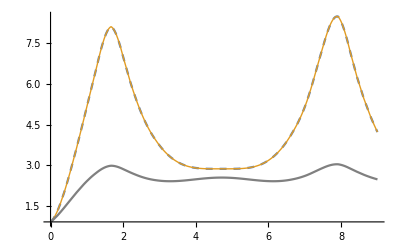

```mathematica
Plot[{phi[2,t],psi[2,t],xi[2,t]},{t,0,9},PlotStyle->{Dashed,Thick,Gray}]
```

```mathematica
Plot3D[phi[z,t],{z,0,2.1},{t,0,7},AxesLabel->Automatic]
```

-Graphics3D-

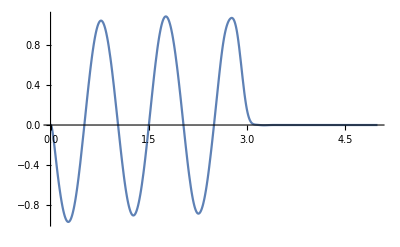

```mathematica
Plot[xi[3,t],{t,0,5},PlotRange->Full]
```